## NetPortGradient

```mathematica
net = NetChain[{LinearLayer[10,"Input"->"Real"],ElementwiseLayer[Tanh],LinearLayer["Output"->"Real"]}];
 netloss = NetGraph[{net,MeanSquaredLossLayer[]},{NetPort["Input"]->NetPort[1,"Input"],NetPort[1,"Output"]->NetPort[2,"Input"]}]
```

NetGraph[<>]

```mathematica
dataset = Table[<|"Input"->x,"Target"->Sin[x]|>,{x,0,10,.1}] ;
```

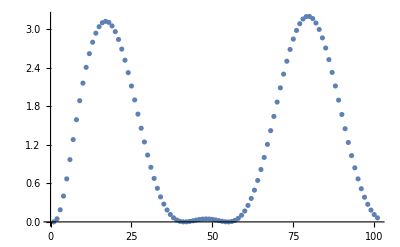

```mathematica
NetInitialize[netloss] /@ dataset //ListPlot
```

```mathematica
trainedNet = NetTrain[netloss,dataset]
```

NetGraph[<>]

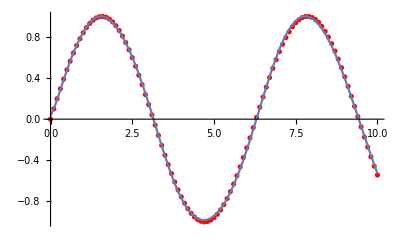

```mathematica
Show[ListPlot[dataset,PlotStyle->Red],Plot[NetExtract[trainedNet,1][x],{x,0,10}]]
```

```mathematica
trainedNet[<|"Input"->.5,"Target"->1|>,NetPortGradient["Input"]]
```

-0.95284

```mathematica
trainedNet[<|"Input"->.5,"Target"->1|>,NetPortGradient["Target"]]
```

1.03284

```mathematica
trainedNet[<|"Input"->.5,"Target"->1|>,NetPortGradient[{1,1,"Weights"}]]
```

{{-0.153471},{-0.075583},{0.000582096},{-0.000244138},{0.0226676},{0.000536104},{-0.264528},{0.0645017},{-0.0211873},{-0.195043}}

```mathematica
trainedNet[<|"Input"->.5,"Target"->1|>,NetPortGradient[{1,3,"Weights"}]]
```

{{0.889434,0.960624,-1.03247,-1.03271,1.01498,-1.03176,0.46802,0.677081,-1.01447,-0.840864}}

```mathematica
trainedNet[<|"Input"->.5,"Target"->1|>,NetPortGradient[All]]
```

<|NetPortGradient[Input]→-0.95284,NetPortGradient[Target]→1.0434,NetPortGradient[{1,1,Biases}]→{-0.33282,-0.158256,0.00111951,-0.000538579,0.0448792,0.00114041,-0.554587,0.142735,-0.0438282,-0.426931},NetPortGradient[{1,1,Weights}]→{{-0.16641},{-0.0791281},{0.000559757},{-0.000269289},{0.0224396},{0.000570203},{-0.277294},{0.0713674},{-0.0219141},{-0.213465}},NetPortGradient[{1,3,Biases}]→{-1.0434},NetPortGradient[{1,3,Weights}]→{{0.886891,0.967511,-1.04306,-1.04326,1.0258,-1.04219,0.424068,0.600908,-1.02443,-0.830927}}|>